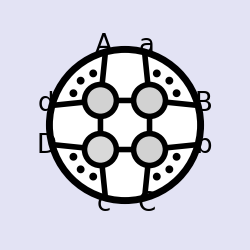
-Graphics-
One-Loop Amplitude Integrands
and Integrals in N=4 SYM
Jacob L. Bourjaily, 2013

```mathematica
<<loop_amplitudes.m
```

```mathematica
capexpand = {ab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] ab[x, a, y] + ab[c, a] ab[x, b, y],
               ab[x___,cap1[{a_,b_},{c__},{d__}],y___]:>(-1)^Length[{y}](ab[x,y,a,c]ab[x,y,b,d]-ab[x,y,a,d]ab[x,y,b,c]),
               ab[a___,cap2[{c_,d_,e_},{f_,g_,h_}],b___]:>ab[a,c,d,b]ab[e,f,g,h]+ab[a,d,e,b]ab[c,f,g,h]+ab[a,e,c,b]ab[d,f,g,h]};
sortab={i_ab:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
ordercup[exp_]:=SortBy[exp,Which[Head[#]===cap,1.5,Head[#]===shift,1.4,True,#]&];
shifexp={ab[x___,shift[y_,z_],w___]:>ab[x,y⟦1⟧,w]+z ab[x,y⟦2⟧,w]};
mom=RandomInteger[{-100,100},{20,4}];
mom1=Table[Binomial[n+i,i],{n,20},{i,0,3}];
neab[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom[[{x}]]];
neab1[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom1[[{x}]]];
randomPositiveZs[n_]:=(Zs=Nest[Function[{mat},Block[{hatted=Append[(Append[Total[mat⟦#1;;-1⟧],1]&)/@Range[2,Length[mat]],Append[PadRight[{},Length[mat⟦1⟧]],1]],newRow=RandomInteger[{1,10},{Length[mat]}]},newRow hatted]],RandomInteger[{1,10},{n+8,1}],3];Zs=Transpose[Inverse[Transpose[Zs⟦{1,2,3,4}⟧]].Transpose[Zs]]⟦5;;-1⟧;)
neabp[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[Zs⟦{x}⟧];
```

```mathematica
dabtoeta=dab[x__]:>Apply[ab,Partition[{x},4,1,5],{1}].η/@{x};
abfactor[exp_]:=Module[{lis=Union@@Cases[exp//.shifexp//.capexpand,_ab,Infinity]/.ab->List},If[Position[exp/(ab@@@Subsets[lis,{4}])//neab,_Integer]=!={},ab@@@Subsets[lis,{4}][[Flatten[Position[exp/(ab@@@Subsets[lis,{4}])//neab,_Integer]]]],exp]];
ordercup2[exp_]:=SortBy[exp,If[Head[#]===cap,If[(#/.cap:>List)[[1]]=={8,9},10,0.5], #]&];

sortR2={i_R:>ordercup2[i]Signature[i]/Signature[ordercup2[i]]};
repR1={R[cap[{a_,b_},{c_,n,n+1}],x___,a_,y___,cap[{n,n+1},m__]]:>(ab[a,b,n,n+1]ab[c,x,a,y])/ab[x,a,y,cap[{n,n+1},{a,b,c}]] R[c,cap[{a,b},{c,n,n+1}],x,a,y]R[a,b,c,n,n+1],R[cap[{b_,a_},{c_,n,n+1}],x___,a_,y___,cap[{n,n+1},m__]]:>(ab[a,b,n,n+1]ab[c,x,a,y])/ab[x,a,y,cap[{n,n+1},{a,b,c}]] R[c,cap[{a,b},{c,n,n+1}],x,a,y]R[a,b,c,n,n+1]};
repR2={R[cap[{a___},{c_,n,n+1}],d___,n+1,cap[{n,n+1},m__]]:>(ab[c,d,n+1]ab[a,n,n+1])/(ab[c,a,n+1]ab[d,n,n+1])R[c,cap[{a},{c,n,n+1}],d,n]R[a,c,n,n+1]};
qlogtodabm={Qlog[ab[7,8,1,i_]/ab[7,8,1,j_]]:>dab[1,i,j,n-1,n]/(ab[1,i,n-1,n] ab[1,j,n-1,n])};
numabfactor[exp_]:=ab@@@Subsets[Range[9],{4}][[Flatten[Position[exp/(ab@@@Subsets[Range[9],{4}])//neab,_Integer]]]];
dabsimp[exp_]:=Module[{f1,f2,f3},f1=exp/.dabcapexpand/.dabtoeta//neab//Simplify;
f2=dab@@(Cases[f1,η[_],Infinity]/.η->List//Flatten);
f3=Times@@(exp/f2/.dabcapexpand/.dabtoeta//neab//Simplify//numabfactor);
If[Abs[( exp/(f2*f3)/.dabcapexpand/.dabtoeta//neab//Simplify)/.i_η:>1//neab]<10,f2*f3 ( exp/(f2*f3)/.dabcapexpand/.dabtoeta//neab//Simplify)/.sortall,exp]
];

absim[exp_]:=Module[{f1},f1=Times@@(exp//numabfactor);
If[Abs[exp/f1//neab]<10,f1(exp/f1//neab),exp]
];
```

```mathematica
Quit[];
```

```mathematica
xitoab={ξ:>(ab[1,2,3,8]ab[1,2,5,6]ab[3,4,7,8])/(ab[8,1,2,cap[{4,3},{5,6,1}]]ab[2,3,7,8]),b:>(ab[1,5,6,8]ab[2,3,7,8])/(ab[5,6,7,8]ab[1,2,3,8]),Subscript[x, 1]:>(1-(ab[1,2,3,4] ab[5,6,7,8])/(ab[1,2,5,6] ab[3,4,7,8])-(ab[3,4,5,6] ab[7,8,1,2])/(ab[1,2,5,6] ab[3,4,7,8])),Subscript[x, 2]:>(ab[1,2,3,4] ab[5,6,7,8])/(ab[1,2,5,6] ab[3,4,7,8])(ab[3,4,5,6] ab[7,8,1,2])/(ab[1,2,5,6] ab[3,4,7,8])};
taure2={τ->(ξ (t^2-Subscript[x, 1]^2+4 Subscript[x, 2]))/(2 (t+Subscript[x, 1]-2 b ξ Subscript[x, 2]))};
(1/ξ+Subscript[x, 1]/τ)^2-(4 Subscript[x, 2])/τ(b+1/τ )==(t/τ+1/ξ)^2;
jacplus3=(ξ (t+Subscript[x, 1]))/(2 (t+Subscript[x, 1]-2 b ξ Subscript[x, 2]));
jacminus3=(ξ (2+b t ξ-b ξ Subscript[x, 1]) Subscript[x, 2])/(t+Subscript[x, 1]-2 b ξ Subscript[x, 2])^2;
shiftm3= shift[{5,6},(((2 ab[1,2,7,8] ab[3,4,8,cap[{1,2},{5,6,8}]])/(ab[1,2,5,8] ab[1,2,6,8] ab[3,4,7,8]))/((2ab[1,2,7,8]ab[6,3,4,cap[{1,2},{5,6,8}]])/(ab[1,2,5,6] ab[1,2,6,8] ab[3,4,7,8])+(t+Subscript[x, 1])) -1)ab[1,2,5,8]/ab[1,2,6,8]];
shiftp3= shift[{5,6},-((t+Subscript[x, 1]+(2ab[1,2,3,4]ab[1,5,7,8]ab[3,4,5,6])/(ab[1,2,5,6] ab[1,3,4,5] ab[3,4,7,8]))ab[1,3,4,5])/((t+Subscript[x, 1]+(2ab[1,2,3,4]ab[1,6,7,8]ab[3,4,5,6])/(ab[1,2,5,6] ab[1,3,4,6] ab[3,4,7,8]))ab[1,3,4,6])];
boxfun3=Li[1]-Li[(t+1-(ab[1,2,7,8]ab[3,4,5,6])/(ab[1,2,5,6]ab[3,4,7,8])-(ab[1,2,3,4]ab[5,6,7,8])/(ab[1,2,5,6]ab[3,4,7,8]))/(t+1+(ab[1,2,7,8]ab[3,4,5,6])/(ab[1,2,5,6]ab[3,4,7,8])-(ab[1,2,3,4]ab[5,6,7,8])/(ab[1,2,5,6]ab[3,4,7,8]))]-Li[(1-(ab[1,2,3,4] ab[1,5,6,8])/(ab[1,2,5,6] ab[1,3,4,8])(-1+t+(ab[1,2,7,8] ab[3,4,5,6])/(ab[1,2,5,6] ab[3,4,7,8])-(ab[1,2,3,4] ab[5,6,7,8])/(ab[1,2,5,6] ab[3,4,7,8])+(2 ab[1,3,4,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[3,4,7,8]))/(1+t-(ab[1,2,7,8] ab[3,4,5,6])/(ab[1,2,5,6] ab[3,4,7,8])+(ab[1,2,3,4] ab[5,6,7,8])/(ab[1,2,5,6] ab[3,4,7,8])-(2 ab[1,2,3,4] ab[1,5,6,8])/(ab[1,2,5,6] ab[1,3,4,8])))]-1/2 log[((t+1-(ab[1,2,7,8]ab[3,4,5,6])/(ab[1,2,5,6]ab[3,4,7,8])-(ab[1,2,3,4]ab[5,6,7,8])/(ab[1,2,5,6]ab[3,4,7,8]))/(t+1+(ab[1,2,7,8]ab[3,4,5,6])/(ab[1,2,5,6]ab[3,4,7,8])-(ab[1,2,3,4]ab[5,6,7,8])/(ab[1,2,5,6]ab[3,4,7,8])))((ab[1,2,3,4] ab[1,5,6,8])/(ab[1,2,5,6] ab[1,3,4,8])(-1+t+(ab[1,2,7,8] ab[3,4,5,6])/(ab[1,2,5,6] ab[3,4,7,8])-(ab[1,2,3,4] ab[5,6,7,8])/(ab[1,2,5,6] ab[3,4,7,8])+(2 ab[1,3,4,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[3,4,7,8]))/(1+t-(2 ab[1,2,3,4] ab[1,5,6,8])/(ab[1,2,5,6] ab[1,3,4,8])-(ab[1,2,7,8] ab[3,4,5,6])/(ab[1,2,5,6] ab[3,4,7,8])+(ab[1,2,3,4] ab[5,6,7,8])/(ab[1,2,5,6] ab[3,4,7,8])))] log[(1-(ab[1,2,3,4] ab[1,5,6,8])/(ab[1,2,5,6] ab[1,3,4,8])(-1+t+(ab[1,2,7,8] ab[3,4,5,6])/(ab[1,2,5,6] ab[3,4,7,8])-(ab[1,2,3,4] ab[5,6,7,8])/(ab[1,2,5,6] ab[3,4,7,8])+(2 ab[1,3,4,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[3,4,7,8]))/(1+t-(2 ab[1,2,3,4] ab[1,5,6,8])/(ab[1,2,5,6] ab[1,3,4,8])-(ab[1,2,7,8] ab[3,4,5,6])/(ab[1,2,5,6] ab[3,4,7,8])+(ab[1,2,3,4] ab[5,6,7,8])/(ab[1,2,5,6] ab[3,4,7,8])))((2(ab[1,2,7,8]ab[3,4,5,6])/(ab[1,2,5,6]ab[3,4,7,8]))/(t+1+(ab[1,2,7,8]ab[3,4,5,6])/(ab[1,2,5,6]ab[3,4,7,8])-(ab[1,2,3,4]ab[5,6,7,8])/(ab[1,2,5,6]ab[3,4,7,8])))]+log[(t+1-(ab[1,2,7,8]ab[3,4,5,6])/(ab[1,2,5,6]ab[3,4,7,8])-(ab[1,2,3,4]ab[5,6,7,8])/(ab[1,2,5,6]ab[3,4,7,8]))/(t+1+(ab[1,2,7,8]ab[3,4,5,6])/(ab[1,2,5,6]ab[3,4,7,8])-(ab[1,2,3,4]ab[5,6,7,8])/(ab[1,2,5,6]ab[3,4,7,8]))] log[1+(ab[1,2,3,4] ab[1,5,6,8])/(ab[1,2,5,6] ab[1,3,4,8])(1-t-(ab[1,2,7,8] ab[3,4,5,6])/(ab[1,2,5,6] ab[3,4,7,8])+(ab[1,2,3,4] ab[5,6,7,8])/(ab[1,2,5,6] ab[3,4,7,8])-(2 ab[1,3,4,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[3,4,7,8]))/(1+t-(2 ab[1,2,3,4] ab[1,5,6,8])/(ab[1,2,5,6] ab[1,3,4,8])-(ab[1,2,7,8] ab[3,4,5,6])/(ab[1,2,5,6] ab[3,4,7,8])+(ab[1,2,3,4] ab[5,6,7,8])/(ab[1,2,5,6] ab[3,4,7,8]))];
```

```mathematica
u2ab[b_,c_]:={ξ:>(ab[1,cap1[{n,2},{b-1,b},{c-1,c}]]ab[2,3,n-1,n])/(ab[1,2,3,n]ab[1,2,c-1,c]ab[b-1,b,n-1,n]),Subscript[τ, u]:>-(ab[1,2,3,n]ab[c-1,c,n-1,n])/(ab[1,c-1,c,n]ab[2,3,n-1,n]),u:>(ab[1,2,b-1,b]ab[c-1,c,n-1,n])/(ab[1,2,c-1,c]ab[b-1,b,n-1,n]),v:>(ab[b-1,b,c-1,c]ab[1,2,n-1,n])/(ab[1,2,c-1,c]ab[b-1,b,n-1,n]),z:>1/2(1+u-v+Sqrt[(1-u-v)^2-4u v]),zb:>1/2(1+u-v-Sqrt[(1-u-v)^2-4u v])};
tau2t={τ:>((t^2+u+t (-1-u+v)) Subscript[τ, u])/(u v+(t-u) ξ Subscript[τ, u])};
boxfun3[b_,c_]:=Li[(t-u)/(t-u+v)]-Li[(ab[1,2,b-1,b] ab[1,c-1,c,n])/(ab[1,2,c-1,c] ab[1,b-1,b,n])(-1+t-u+v+(ab[1,b-1,b,n] ab[c-1,c,n-1,n])/(ab[1,c-1,c,n] ab[b-1,b,n-1,n]))/(t-(ab[1,2,b-1,b] ab[1,c-1,c,n])/(ab[1,2,c-1,c] ab[1,b-1,b,n]))]+1/2 log[(t-u)/(t-u+v) (ab[1,2,b-1,b] ab[1,c-1,c,n])/(ab[1,2,c-1,c] ab[1,b-1,b,n])(-1+t-u+v+(ab[1,b-1,b,n] ab[c-1,c,n-1,n])/(ab[1,c-1,c,n] ab[b-1,b,n-1,n]))/(t-(ab[1,2,b-1,b] ab[1,c-1,c,n])/(ab[1,2,c-1,c] ab[1,b-1,b,n]))]log[(1-(t-u)/(t-u+v))/(1-(ab[1,2,b-1,b] ab[1,c-1,c,n])/(ab[1,2,c-1,c] ab[1,b-1,b,n])(-1+t-u+v+(ab[1,b-1,b,n] ab[c-1,c,n-1,n])/(ab[1,c-1,c,n] ab[b-1,b,n-1,n]))/(t-(ab[1,2,b-1,b] ab[1,c-1,c,n])/(ab[1,2,c-1,c] ab[1,b-1,b,n])))];
```

```mathematica
h3[b_,c_]:=dlog[((t-u+(ab[1,2,-1+b,b] ab[1,-1+c,-1+n,n] ab[-1+b,b,-1+c,c])/(ab[1,2,-1+c,c] ab[1,-1+b,b,-1+c] ab[-1+b,b,-1+n,n])) (-1+t+v-ξ Subscript[τ, u]))/((t-u) (t-u-(ab[1,2,-1+n,n] ab[cap[{1,2},{-1+c,c,n}],-1+b,b,-1+c])/(ab[1,2,-1+c,c] ab[1,2,-1+c,n] ab[-1+b,b,-1+n,n])))] Qlog[ab[1,2,-1+n,n]/ab[1,-1+c,-1+n,n]] R[1,2,-1+b,b,-1+c]+dlog[((t-u) (t-u-(ab[1,2,-1+n,n] ab[cap[{1,2},{-1+c,c,n}],-1+b,b,c])/(ab[1,2,-1+c,c] ab[1,2,c,n] ab[-1+b,b,-1+n,n])))/((t-u+(ab[1,2,-1+b,b] ab[1,c,-1+n,n] ab[-1+b,b,-1+c,c])/(ab[1,2,-1+c,c] ab[1,-1+b,b,c] ab[-1+b,b,-1+n,n])) (-1+t+v-ξ Subscript[τ, u]))] Qlog[ab[1,2,-1+n,n]/ab[1,c,-1+n,n]] R[1,2,-1+b,b,c]+dlog[((t-u) (t-u+(ab[1,2,-1+b,b] ab[1,2,-1+n,n] ab[-1+b,-1+c,c,n])/(ab[1,2,-1+b,n] ab[1,2,-1+c,c] ab[-1+b,b,-1+n,n])))/((t-u+(ab[1,cap[{-1+c,c},{1,2,-1+b}],-1+n,n] ab[-1+b,b,-1+c,c])/(ab[1,2,-1+c,c] ab[1,-1+b,-1+c,c] ab[-1+b,b,-1+n,n])) (-1+t+v-ξ Subscript[τ, u]))] Qlog[ab[1,cap[{-1+c,c},{1,2,-1+b}],-1+n,n]/ab[1,2,-1+n,n]] R[1,2,-1+b,-1+c,c]+dlog[((t-u+(ab[1,cap[{-1+c,c},{1,2,b}],-1+n,n] ab[-1+b,b,-1+c,c])/(ab[1,2,-1+c,c] ab[1,b,-1+c,c] ab[-1+b,b,-1+n,n])) (-1+t+v-ξ Subscript[τ, u]))/((t-u) (t-u+(ab[1,2,-1+b,b] ab[1,2,-1+n,n] ab[b,-1+c,c,n])/(ab[1,2,b,n] ab[1,2,-1+c,c] ab[-1+b,b,-1+n,n])))] Qlog[ab[1,cap[{-1+c,c},{1,2,b}],-1+n,n]/ab[1,2,-1+n,n]] R[1,2,b,-1+c,c]+dlog[((t-u) (t-u+(u v)/(ξ Subscript[τ, u])))/(-1+t+v-ξ Subscript[τ, u])] Qlog[ab[1,cap[{-1+c,c},{1,-1+b,b}],-1+n,n]/ab[1,2,-1+n,n]] R[1,-1+b,b,-1+c,c]+dlog[((t-u-ab[1,cap[{-1+c,c},{2,-1+b,b}],-1+n,n]/(ab[1,2,-1+c,c] ab[-1+b,b,-1+n,n])) (-1+t+v-ξ Subscript[τ, u]))/((t-u) (t-u+(ab[1,2,-1+b,b] ab[1,2,-1+n,n] ab[2,-1+c,c,n] ab[-1+b,b,-1+c,c])/(ab[1,2,-1+c,c] ab[1,cap[{-1+b,b},{-1+c,c,2}],2,n] ab[-1+b,b,-1+n,n])))] Qlog[ab[1,cap[{-1+c,c},{2,-1+b,b}],-1+n,n]/ab[1,2,-1+n,n]] R[2,-1+b,b,-1+c,c];
```

```mathematica
Clear[h3]
```

```mathematica
Clear[boxfun3]
```

```mathematica
Clear[n];
```

```mathematica
todmatrixn
```

FuseDmatrices[#1/.i_R:>fromRform[n][i]⟦1,1⟧ Dmatrix[fromRform[n][i]⟦1,2⟧]//.shifexp//.capexpand]&

```mathematica
n=9;
```

```mathematica
f246=fuse[((First[rForm[onShellGraph[2][{{2,3},{4,5},{6,7,8,9},{10,1}},{0,0,0,0}]]]/.sortR/.Rtodab//todmatrix//fullabB)/.dabBexp/.dabshifexp/.sortall)//todoubleab]//neabp;
```

```mathematica
f246p=Limit[Simplify[Simplify[f246/.dabne[{2,3}]/.DmatrixEval3[{1,1,1},3],e>0&&τ>0]/.Sqrt[x_]:>Sqrt[Limit[x,e->0]],τ>0],e->0];
```

```mathematica
Simplify[Simplify[f246p,τ>0]/.tau2t/.u2ab[4,6]//neabp,t>neabp[z//.u2ab[4,6]]]*D[τ/.tau2t,t]/.u2ab[4,6]//neabp//Simplify
```

-(643505923795 (18803427+1604885 t)^2)/(5612468 (2432907+88268675 t) (-8110431+230782463 t) (-6491457+2389673765 t))

```mathematica
f246m=Limit[Simplify[Simplify[f246/.dabne[{2,3}]/.DmatrixEval3[{1,1,1},3]/.Sqrt[x_]:>-Sqrt[x],e>0&&τ>0]/.Sqrt[x_]:>Sqrt[Limit[x,e->0]],τ>0],e->0];
```

```mathematica
Simplify[Simplify[f246m,τ>0]/.tau2t/.u2ab[4,6]//neabp,t>neabp[z//.u2ab[4,6]]]*D[τ/.tau2t,t]/.u2ab[4,6]//neabp//Simplify
```

(124217645395269897415 (11351323-2061899605 t)^2)/(5804 (2969695+53603159 t) (-326649521+5413277105 t) (-8121878819+11730104465 t) (-244924702+45772925085 t))

```mathematica
%521-%523//Factor
```

-((643505923795 (-679190325129169616533881387820957546267090555911+125138059939975206711197104598012805334277526463770 t+724437467754684207493238059682425700417864556520385 t^2-69744399889906745211030005093190830864936391204582100 t^3-774665785035828283748291241316849654922450310720008125 t^4+38640505885562753404707332924770201661714024372220776250 t^5+401281396523536642807809253251892011261697813471875 t^6))/(5612468 (2969695+53603159 t) (2432907+88268675 t) (-8110431+230782463 t) (-6491457+2389673765 t) (-326649521+5413277105 t) (-8121878819+11730104465 t) (-244924702+45772925085 t)))

```mathematica
fuse[h3[4,6]/.qlogtodab/.dabcapexpand//todmatrix//todoubleab]/.dlog[x_]:>D[Log[x],t]//.u2ab[4,6]/.dabne[{2,3}]/.DmatrixEval3[{1,1,1},3]//neabp//Factor
```

-((7706657770 (-679190325129169616533881387820957546267090555911+125138059939975206711197104598012805334277526463770 t+724437467754684207493238059682425700417864556520385 t^2-69744399889906745211030005093190830864936391204582100 t^3-774665785035828283748291241316849654922450310720008125 t^4+38640505885562753404707332924770201661714024372220776250 t^5+401281396523536642807809253251892011261697813471875 t^6))/(967 (2969695+53603159 t) (2432907+88268675 t) (-8110431+230782463 t) (-6491457+2389673765 t) (-326649521+5413277105 t) (-8121878819+11730104465 t) (-244924702+45772925085 t)))

```mathematica
(%542)/(%544)//Simplify
```

11608/167

```mathematica
ab[1,2,3,9]/ab[2,3,8,9]//neabp
```

167/11608

```mathematica
(D[h3[4,6],R[1,2,3,4,5]]/.Qlog[x_]:>1)boxfun3[4,6]/.dlog[x_]:>
```

dlog[((t-u+(ab[1,2,3,4] ab[1,5,8,9] ab[3,4,5,6])/(ab[1,2,5,6] ab[1,3,4,5] ab[3,4,8,9])) (-1+t+v-ξ τ_u))/((t-u) (t-u-(ab[1,2,8,9] ab[cap[{1,2},{5,6,9}],3,4,5])/(ab[1,2,5,6] ab[1,2,5,9] ab[3,4,8,9])))] (Li[(t-u)/(t-u+v)]-Li[(ab[1,2,3,4] ab[1,5,6,9] (-1+t-u+v+(ab[1,3,4,9] ab[5,6,8,9])/(ab[1,5,6,9] ab[3,4,8,9])))/(ab[1,2,5,6] ab[1,3,4,9] (t-(ab[1,2,3,4] ab[1,5,6,9])/(ab[1,2,5,6] ab[1,3,4,9])))]+1/2 log[((t-u) ab[1,2,3,4] ab[1,5,6,9] (-1+t-u+v+(ab[1,3,4,9] ab[5,6,8,9])/(ab[1,5,6,9] ab[3,4,8,9])))/((t-u+v) ab[1,2,5,6] ab[1,3,4,9] (t-(ab[1,2,3,4] ab[1,5,6,9])/(ab[1,2,5,6] ab[1,3,4,9])))] log[(1-(t-u)/(t-u+v))/(1-(ab[1,2,3,4] ab[1,5,6,9] (-1+t-u+v+(ab[1,3,4,9] ab[5,6,8,9])/(ab[1,5,6,9] ab[3,4,8,9])))/(ab[1,2,5,6] ab[1,3,4,9] (t-(ab[1,2,3,4] ab[1,5,6,9])/(ab[1,2,5,6] ab[1,3,4,9]))))])

```mathematica
Limit[f246m-f246p,τ->0]//Simplify
```

63270484104434014757321/(6604360987906249884 √23750102917)

```mathematica
(scalarBoxIntegral[{{2,3},{4,5},{6,7,8,9},{10,1}}]//fullabB//neabp)/.{Li[x_]:>Li[Simplify[Limit[x,e->0],τ>0]],log[x_]:>Log[Simplify[Limit[x,e->0],τ>0]]}/.Li[x_]:>PolyLog[2,x]
```

-π^2/6+1/2 Log[9689340/(268015795+7864134153 τ)] Log[(894285+415019373 τ)/(268015795+7864134153 τ)]-Log[(138405425+3724557390 τ+√5 √(3311833101261065+190959925477130496 τ+2774465550280722420 τ^2))/(268015795+7864134153 τ)] Log[(129610370+4139576763 τ+√5 √(3311833101261065+190959925477130496 τ+2774465550280722420 τ^2))/(268015795+7864134153 τ)]+PolyLog[2,(138405425+3724557390 τ+√5 √(3311833101261065+190959925477130496 τ+2774465550280722420 τ^2))/(268015795+7864134153 τ)]+PolyLog[2,(129610370+4139576763 τ+√5 √(3311833101261065+190959925477130496 τ+2774465550280722420 τ^2))/(268015795+7864134153 τ)]

```mathematica
NIntegrate[%555*%574,{τ,0,Infinity},WorkingPrecision->40,PrecisionGoal->35]
```

1.058624029061465512886939901448565761452×10^168860

```mathematica
Li[1]/.Li[x_]:>PolyLog[x,2]
```

-ⅈ π

```mathematica
PolyLog[2,1]
```

π^2/6